```mathematica
(*tropical plot*)
p=8x+2y+5 (*a multivariate polynomial*)
```

5+8 x+2 y

```mathematica
MinPlus[poly_]:=ReplaceAll[poly,(*This function takes a polynomial as an argument and applies the MinPlus algebra on it*){Plus->Min,Times->Plus,Power->Times}];
MaxPlus[poly_]:=ReplaceAll[poly,(*This function takes a polynomial as an argument and applies the MinPlus algebra on it*){Plus->Max,Times->Plus,Power->Times}];
```

```mathematica
MinPlus[p]  (*applied MinPlus algebra on a polynomial p*)
```

Min[5,8+x,2+y]

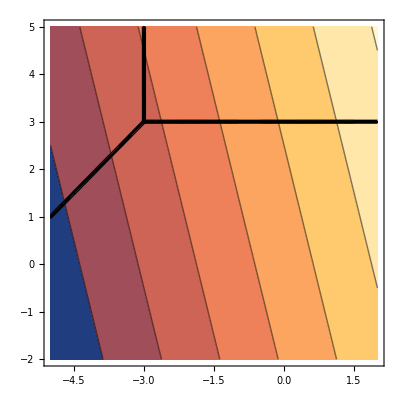

```mathematica
ContourPlot[MinPlus[p],{x,-5,2},{y,-2,5},ExclusionsStyle->Black]
```

```mathematica
MaxPlus[p]
```

Max[5,8+x,2+y]

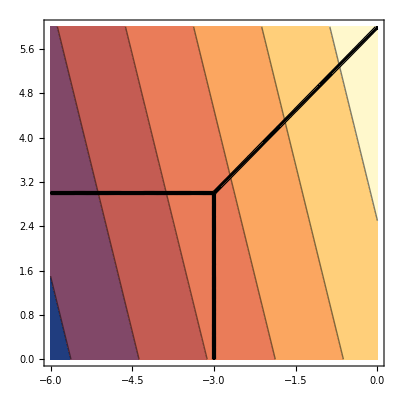

```mathematica
ContourPlot[MaxPlus[p],{x,-6,0},{y,0,6},ExclusionsStyle->Black]
```

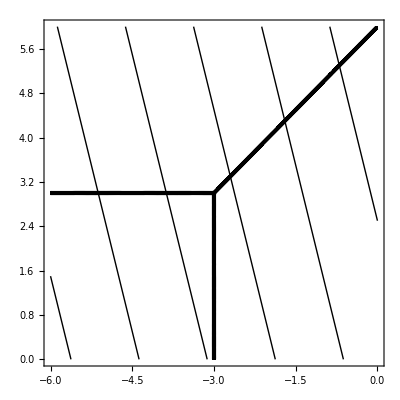

```mathematica
ContourPlot[MaxPlus[p],{x,-6,0},{y,0,6},ContourShading->None,ExclusionsStyle->Black]
```

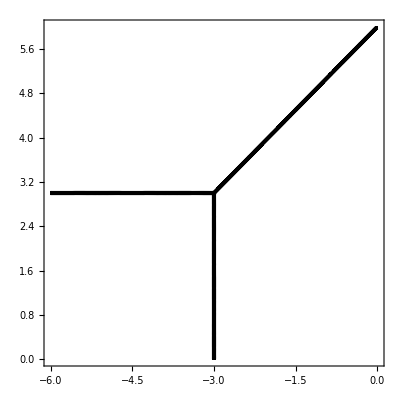

```mathematica
ContourPlot[MaxPlus[p],{x,-6,0},{y,0,6},ContourStyle->Directive[GrayLevel[0],Opacity[0.],AbsoluteThickness[0.],Dotted],ContourShading->None,ExclusionsStyle->Black]
```

```mathematica
(*tropicalization*)
valuation=IntegerExponent[#,2]&/@Last/@CoefficientRules[p,{x,y}] (*this function brings the valuation of every coefficient*)
```

{3,1,0}

```mathematica
TropicalMinPlusPoly[poly_,variables_]:=Min@@(Flatten/@Transpose[{First/@CoefficientRules[poly,variables],IntegerExponent[#,2]&/@Last/@CoefficientRules[poly,variables]}].Append[variables,1])
TropicalMaxPlusPoly[poly_,variables_]:=Max@@(Flatten/@Transpose[{First/@CoefficientRules[poly,variables],IntegerExponent[#,2]&/@Last/@CoefficientRules[poly,variables]}].Append[variables,1])
```

```mathematica
TropicalMinPlusPoly[p,{x,y}]
```

Min[0,3+x,1+y]

```mathematica
f = TropicalMaxPlusPoly[p, {x,y}]
```

Max[0,3+x,1+y]

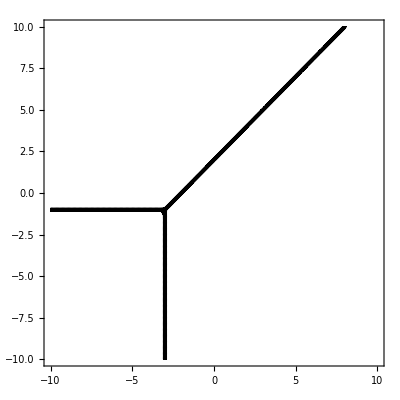

```mathematica
ContourPlot[f,{x,-10, 10},{y,-10,10},ContourStyle->Directive[GrayLevel[0],Opacity[0.],AbsoluteThickness[0.],Dotted],ContourShading->None,ExclusionsStyle->Black]
```

```mathematica
(*Newton Polytope*)
NewtonPolytope[poly_,variables_]:=Module[{tpoly,p,cs,P2=poly},p=First/@CoefficientRules[P2,variables];
cs=IntegerExponent[#,2]&/@Last/@CoefficientRules[P2,variables];
tpoly=Flatten/@Transpose[{p,cs}];
Show[ListPlot3D[tpoly,Mesh->All,Axes->True,PlotStyle->{Yellow},Filling->Bottom],ListPointPlot3D[tpoly]]]
```

```mathematica
NewtonPolytope[16x^2+6x y+7y^2+7x+5y+2,{x,y}]
```

-Graphics3D-

```mathematica
NewtonPolytope[p,{x,y}]
```

-Graphics3D-

```mathematica
(*Puiseux series and valuations*)
PuiseuxValuation[expr_]:=Exponent[expr,t,List]/. {e:{__}:>Min[e],{}->-Infinity};

PuiseuxValuation[1/t-4/t^2+5 t^2+t^20]
PuiseuxValuation[8 t^6+t^20+t^7]
PuiseuxValuation[0]
PuiseuxValuation[30t^(94/3) - 59/(t^(98/5))]
(*-2 6-∞ -98/5*)
```

-2

6

-∞

-98/5

```mathematica
TropicalPuiseuxPoly[poly_,variables_]:=Max@@(Flatten/@Transpose[{First/@CoefficientRules[poly,variables],-PuiseuxValuation/@MonomialList[poly, variables]}].Append[variables,1])
```

```mathematica
f=(t^(-1)+1)x+(t^(2)-3t^(3))y+5t^(4)
PuiseuxValuation/@MonomialList[f, {x,y}]
```

5 t^4+(1+1/t) x+(t^2-3 t^3) y

{-1,2,4}

```mathematica
ff = TropicalPuiseuxPoly[f, {x,y}]
```

Max[-4,1+x,-2+y]

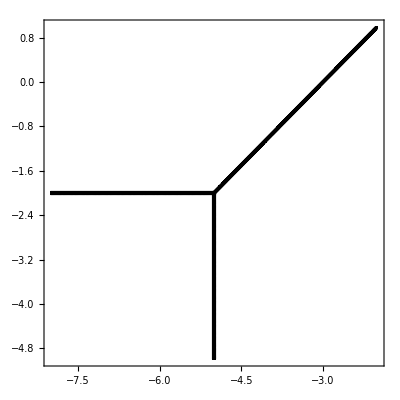

```mathematica
(*Exercises*)
ContourPlot[ff,{x,-8, -2},{y,-5, 1},ContourStyle->Directive[GrayLevel[0],Opacity[0.],AbsoluteThickness[0.],Dotted],ContourShading->None,ExclusionsStyle->Black]
```

```mathematica
g = t^(3)x^(2)+2x*y+t*y^(2)+(t+t^(3))*x-5y+1
```

1+(t+t^3) x+t^3 x^2-5 y+2 x y+t y^2

```mathematica
gg = TropicalPuiseuxPoly[g, {x,y}]
```

Max[0,-1+x,-3+2 x,y,x+y,-1+2 y]

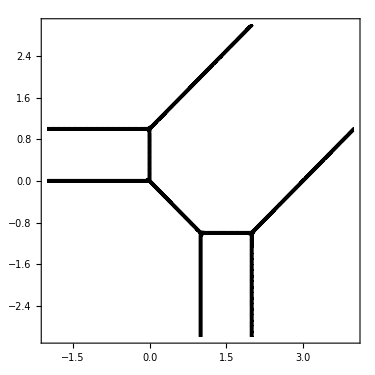

```mathematica
ContourPlot[gg,{x,-2,4},{y,-3,3},ContourStyle->Directive[GrayLevel[0],Opacity[0.],AbsoluteThickness[0.],Dotted],ContourShading->None,ExclusionsStyle->Black]
```

```mathematica
h=x*y+t*(y+x+x^(2)+x^(2)y^(2))+t^(3)
```

t^3+x y+t (x+x^2+y+x^2 y^2)

```mathematica
hh = TropicalPuiseuxPoly[h, {x,y}]
```

Max[-3,-1+x,-1+2 x,-1+y,x+y,-1+2 x+2 y]

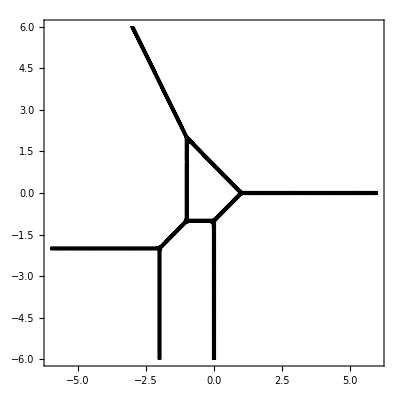

```mathematica
ContourPlot[hh,{x,-6,6},{y,-6,6},ContourStyle->Directive[GrayLevel[0],Opacity[0.],AbsoluteThickness[0.],Dotted],ContourShading->None,ExclusionsStyle->Black]
```

```mathematica
f1 = 144(x^(4)+y^(3))-32(x+y^(2))+350x^(2)y^(2)+80
```

80+350 x^2 y^2-32 (x+y^2)+144 (x^4+y^3)

```mathematica
ff1 = TropicalMaxPlusPoly[f1, {x,y}]
```

```mathematica
Max[4,5+x,4+4 x,5+2 y,1+2 x+2 y,4+3 y]
```

Max[4,5+x,4+4 x,5+2 y,1+2 x+2 y,4+3 y]

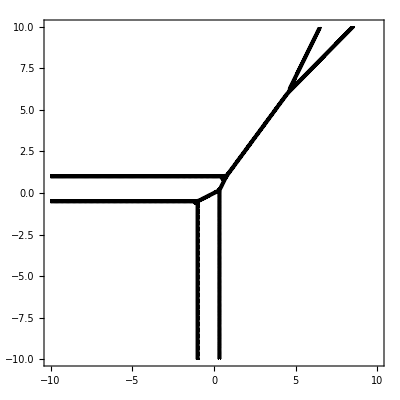

```mathematica
ContourPlot[ff1,{x,-10,10},{y,-10,10},ContourStyle->Directive[GrayLevel[0],Opacity[0.],AbsoluteThickness[0.],Dotted],ContourShading->None,ExclusionsStyle->Black]
```